```mathematica
SetDirectory[NotebookDirectory[]];
matr=Partition[Delete[ReadList["./data/zeroPt.txt", Real], 1], 2];
```

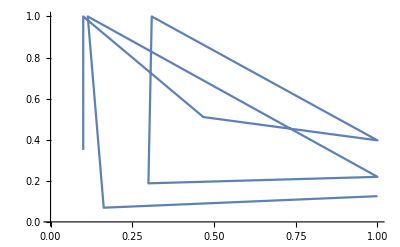

```mathematica
ListLinePlot[matr]
```

```mathematica
Animate[ListLinePlot[matr[[i]]],{i,1,Length[matr],1}]
```